# Light front wave function data

## 05/28/2022 - Pion data, see “state[0,1]” - Basis functions definitions

## Model Parameters

```mathematica
cwd = NotebookDirectory[]

ALPHAS=0.89;  (*strong coupling*)
QUARK=0.48;  (*quark mass*)
KAPPA=0.61; (*confinement strengh*)
NMAX=8; (*Transverse cutoff*)
LMAX=24; (*Longitudinal cutoff*)
MUG=0.02; (*Regulator cutoff*)
ALPHA=(4 QUARK^2)/KAPPA^2;(*Equal mass case*)
BETA=ALPHA;(*Equal mass case*)

fs=40;(*fontsize*)

spinlabel[tots_,projs_]:=
Which[{tots,projs}=={1,1},"↑↑",{tots,projs}=={1,-1},"↓↓",{tots,projs}=={1,0},"↑↓+↓↑",{tots,projs}=={0,0},"↑↓-↓↑"];
spinlabel2[spins_]:=
Which[spins=={1,1},"↑↑",spins=={-1,-1},"↓↓",spins=={1,-1},"↑↓",spins=={-1,1},"↓↑"];
coeffspin[state_,{s1_,s2_}]:=Module[{result},
result={};
Do[If[state[[i,4]]==s1 && state[[i,5]]==s2,AppendTo[result,state[[i]]],0],{i,Length[state]}];
result] (*collect all the coefficient for the specifc spin config*)

timeSince[t_]:=Print["Elapsed time: "<>ToString[AbsoluteTime[]-t]<>"s"]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\LFWF_data\

## Loading data files (Do not run this part!)

### - Each data file corresponds to a different mJ, magnetic projection - Each row is a basis function with columns of n, m, l, s1, s2, coeff1, coeff2, ..., coeff50 - For calculating pion’s LFWF, you want to use mJ=0 file with coeff=coeff1, which is state[0,1] defined below.

```mathematica
SetDirectory[NotebookDirectory[]]
fileDirectory = NotebookDirectory[]<>"BLFQ_LFWF_pion";
cvt[x_]:=ToString[IntegerPart[Mod[x,10]]]<>"p"<>ToString[IntegerPart[Mod[x*10,10]]]<>ToString[IntegerPart[Mod[x*100,10]]];
data[0]=Import[fileDirectory<>"/evect_a0p89_mf0p48_kap0p61_mJ0_mug0.02_grid64_N8_L24_lambda0p56.dat","Table"];(*mj=0 data*)
data[1]=Import[fileDirectory<>"/evect_a0p89_mf0p48_kap0p61_mJ1_mug0.02_grid64_N8_L24_lambda0p56.dat","Table"];(*mj=1 data*)
data[-1]=Import[fileDirectory<>"/evect_a0p89_mf0p48_kap0p61_mJm1_mug0.02_grid64_N8_L24_lambda0p56.dat","Table"];(*mj=-1 data*)
stategen[mJ_,which_]:=data[mJ][[All,{1,2,3,4,5,which+5}]]; (*collect all the basis quantum number and coefficients for the desired state*)
Do[state[0,i]=stategen[0,i],{i,1,20}]; (*storing*)
Do[state[1,i]=stategen[1,i],{i,1,20}]; (*storing*)
Do[state[-1,i]=stategen[-1,i],{i,1,20}]; (*storing*)
Normality[array_]:=Sum[Abs[array[[i,6]]]^2,{i,1,Length[array]}];
Print["Number of States: " ,Dimensions[data[0]][[2]]-5]
Print["Number of Basis Functions: ",Dimensions[data[0]][[1]]]
Print["Sum of C_i squared = ",NumberForm[Normality[state[0,1]],10], " for the 1st state at m_J=0"]
Print["Sum of C_i squared = ",NumberForm[Normality[state[0,2]],10], " for the 2nd state at m_J=0"]
Print["Sum of C_i squared = ",NumberForm[Normality[state[0,3]],10], " for the 3rd state at m_J=0"]
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\OniumV2_Calculation

Number of States: 50

Number of Basis Functions: 400

Sum of C_i squared = 1.000000001 for the 1st state at m_J=0

Sum of C_i squared = 0.9999999919 for the 2nd state at m_J=0

Sum of C_i squared = 1.000000017 for the 3rd state at m_J=0

## The complete Pion (mJ=0) light-front wave functions:

### - Each row is a basis function with entries of n, m, l, s1, s2, coefficient

```mathematica
(*Everything you need for Pion LFWF is exported here*)
state[0,1]={{0,1,0,-1,-1,-0.29865025},{0,1,1,-1,-1,-5.784796*^-16},{0,1,2,-1,-1,-0.06975905},{0,1,3,-1,-1,-5.0202301*^-16},{0,1,4,-1,-1,-0.022885298},{0,1,5,-1,-1,-1.6222933*^-16},{0,1,6,-1,-1,-0.0090790754},{0,1,7,-1,-1,7.3552479*^-17},{0,1,8,-1,-1,-0.0041498752},{0,1,9,-1,-1,2.2015332*^-16},{0,1,10,-1,-1,-0.0021267303},{0,1,11,-1,-1,3.6972683*^-16},{0,1,12,-1,-1,-0.0011989873},{0,1,13,-1,-1,4.9252189*^-16},{0,1,14,-1,-1,-0.00073183349},{0,1,15,-1,-1,7.6229989*^-16},{0,1,16,-1,-1,-0.00047656358},{0,1,17,-1,-1,1.5984802*^-15},{0,1,18,-1,-1,-0.00032662761},{0,1,19,-1,-1,4.0841478*^-16},{0,1,20,-1,-1,-0.00023282766},{0,1,21,-1,-1,-1.316906*^-14},{0,1,22,-1,-1,-0.00017092997},{0,1,23,-1,-1,3.1884371*^-14},{0,1,24,-1,-1,-0.00012829913},{1,1,0,-1,-1,0.22019838},{1,1,1,-1,-1,2.9310326*^-16},{1,1,2,-1,-1,0.060777844},{1,1,3,-1,-1,5.2506316*^-16},{1,1,4,-1,-1,0.022137361},{1,1,5,-1,-1,1.8897569*^-16},{1,1,6,-1,-1,0.0093959541},{1,1,7,-1,-1,-7.6058683*^-17},{1,1,8,-1,-1,0.0044869367},{1,1,9,-1,-1,-2.4713968*^-16},{1,1,10,-1,-1,0.0023617684},{1,1,11,-1,-1,-4.3311168*^-16},{1,1,12,-1,-1,0.0013504455},{1,1,13,-1,-1,-5.9027573*^-16},{1,1,14,-1,-1,0.00082861942},{1,1,15,-1,-1,-9.561541*^-16},{1,1,16,-1,-1,0.00053937253},{1,1,17,-1,-1,-2.1082445*^-15},{1,1,18,-1,-1,0.00036838954},{1,1,19,-1,-1,-4.5069011*^-16},{1,1,20,-1,-1,0.00026134297},{1,1,21,-1,-1,1.8440517*^-14},{1,1,22,-1,-1,0.0001908967},{1,1,23,-1,-1,-4.4407914*^-14},{1,1,24,-1,-1,0.00014258214},{2,1,0,-1,-1,-0.1522439},{2,1,1,-1,-1,-2.2461901*^-16},{2,1,2,-1,-1,-0.048060128},{2,1,3,-1,-1,-4.9001109*^-16},{2,1,4,-1,-1,-0.019091739},{2,1,5,-1,-1,-2.2233806*^-16},{2,1,6,-1,-1,-0.0085775302},{2,1,7,-1,-1,4.7600302*^-17},{2,1,8,-1,-1,-0.0042522151},{2,1,9,-1,-1,2.0322638*^-16},{2,1,10,-1,-1,-0.0022907274},{2,1,11,-1,-1,3.8282871*^-16},{2,1,12,-1,-1,-0.001325868},{2,1,13,-1,-1,5.6600507*^-16},{2,1,14,-1,-1,-0.00081663515},{2,1,15,-1,-1,1.0052846*^-15},{2,1,16,-1,-1,-0.000530473},{2,1,17,-1,-1,2.3669582*^-15},{2,1,18,-1,-1,-0.00036027203},{2,1,19,-1,-1,3.6102832*^-16},{2,1,20,-1,-1,-0.00025371091},{2,1,21,-1,-1,-2.2414848*^-14},{2,1,22,-1,-1,-0.00018388599},{2,1,23,-1,-1,5.3520324*^-14},{2,1,24,-1,-1,-0.00013631638},{3,1,0,-1,-1,0.10231557},{3,1,1,-1,-1,1.5219233*^-16},{3,1,2,-1,-1,0.03601927},{3,1,3,-1,-1,4.1598498*^-16},{3,1,4,-1,-1,0.015492275},{3,1,5,-1,-1,2.310175*^-16},{3,1,6,-1,-1,0.0073396821},{3,1,7,-1,-1,2.4318697*^-17},{3,1,8,-1,-1,0.0037634112},{3,1,9,-1,-1,-1.0958868*^-16},{3,1,10,-1,-1,0.0020669692},{3,1,11,-1,-1,-2.3586575*^-16},{3,1,12,-1,-1,0.0012062505},{3,1,13,-1,-1,-4.4343381*^-16},{3,1,14,-1,-1,0.00074285783},{3,1,15,-1,-1,-9.3087157*^-16},{3,1,16,-1,-1,0.00047970231},{3,1,17,-1,-1,-2.4422606*^-15},{3,1,18,-1,-1,0.00032280048},{3,1,19,-1,-1,-1.5920789*^-16},{3,1,20,-1,-1,0.00022497505},{3,1,21,-1,-1,2.5724886*^-14},{3,1,22,-1,-1,0.00016144923},{3,1,23,-1,-1,-6.0658288*^-14},{3,1,24,-1,-1,0.00011867514},{0,0,0,-1,1,-0.4424662},{0,0,1,-1,1,9.7838404*^-16},{0,0,2,-1,1,-0.14185452},{0,0,3,-1,1,-1.9081958*^-15},{0,0,4,-1,1,-0.057351761},{0,0,5,-1,1,-2.2135072*^-15},{0,0,6,-1,1,-0.026806755},{0,0,7,-1,1,-2.4008573*^-15},{0,0,8,-1,1,-0.014001358},{0,0,9,-1,1,-2.402592*^-15},{0,0,10,-1,1,-0.007993633},{0,0,11,-1,1,-2.3748364*^-15},{0,0,12,-1,1,-0.0049080662},{0,0,13,-1,1,-2.6372134*^-15},{0,0,14,-1,1,-0.0031985422},{0,0,15,-1,1,-2.2785593*^-15},{0,0,16,-1,1,-0.0021876932},{0,0,17,-1,1,-2.972015*^-15},{0,0,18,-1,1,-0.0015552247},{0,0,19,-1,1,-3.307684*^-15},{0,0,20,-1,1,-0.0011396918},{0,0,21,-1,1,-4.1778647*^-15},{0,0,22,-1,1,-0.0008551627},{0,0,23,-1,1,-3.8784297*^-14},{0,0,24,-1,1,-0.00065372247},{1,0,0,-1,1,0.23473397},{1,0,1,-1,1,-1.2490009*^-16},{1,0,2,-1,1,0.085603842},{1,0,3,-1,1,1.4814538*^-15},{1,0,4,-1,1,0.038633527},{1,0,5,-1,1,1.7451318*^-15},{1,0,6,-1,1,0.019479898},{1,0,7,-1,1,1.8873791*^-15},{1,0,8,-1,1,0.010718722},{1,0,9,-1,1,1.9459261*^-15},{1,0,10,-1,1,0.0063410899},{1,0,11,-1,1,1.9311809*^-15},{1,0,12,-1,1,0.0039868767},{1,0,13,-1,1,2.1733917*^-15},{1,0,14,-1,1,0.0026381386},{1,0,15,-1,1,1.8310006*^-15},{1,0,16,-1,1,0.0018213188},{1,0,17,-1,1,2.5645718*^-15},{1,0,18,-1,1,0.0013017235},{1,0,19,-1,1,2.5543803*^-15},{1,0,20,-1,1,0.00095657765},{1,0,21,-1,1,1.735374*^-15},{1,0,22,-1,1,0.00071857616},{1,0,23,-1,1,3.422772*^-14},{1,0,24,-1,1,0.00054929429},{2,0,0,-1,1,-0.1335192},{2,0,1,-1,1,1.6132928*^-16},{2,0,2,-1,1,-0.054676901},{2,0,3,-1,1,-9.5756736*^-16},{2,0,4,-1,1,-0.026913104},{2,0,5,-1,1,-1.3045121*^-15},{2,0,6,-1,1,-0.014429835},{2,0,7,-1,1,-1.4571677*^-15},{2,0,8,-1,1,-0.0082946252},{2,0,9,-1,1,-1.5278577*^-15},{2,0,10,-1,1,-0.0050601664},{2,0,11,-1,1,-1.5118115*^-15},{2,0,12,-1,1,-0.0032486905},{2,0,13,-1,1,-1.7857352*^-15},{2,0,14,-1,1,-0.002178776},{2,0,15,-1,1,-1.4129323*^-15},{2,0,16,-1,1,-0.0015162383},{2,0,17,-1,1,-2.1787043*^-15},{2,0,18,-1,1,-0.0010882206},{2,0,19,-1,1,-1.8242786*^-15},{2,0,20,-1,1,-0.00080106018},{2,0,21,-1,1,6.108395*^-16},{2,0,22,-1,1,-0.00060188975},{2,0,23,-1,1,-2.9833991*^-14},{2,0,24,-1,1,-0.0004597756},{3,0,0,-1,1,0.078487416},{3,0,1,-1,1,2.6020852*^-18},{3,0,2,-1,1,0.035171637},{3,0,3,-1,1,6.5572547*^-16},{3,0,4,-1,1,0.018730191},{3,0,5,-1,1,9.2807706*^-16},{3,0,6,-1,1,0.010632825},{3,0,7,-1,1,1.0720591*^-15},{3,0,8,-1,1,0.0063611796},{3,0,9,-1,1,1.1359186*^-15},{3,0,10,-1,1,0.0039877816},{3,0,11,-1,1,1.1340755*^-15},{3,0,12,-1,1,0.0026060422},{3,0,13,-1,1,1.3867488*^-15},{3,0,14,-1,1,0.0017666657},{3,0,15,-1,1,1.0041881*^-15},{3,0,16,-1,1,0.0012366094},{3,0,17,-1,1,1.8032722*^-15},{3,0,18,-1,1,0.00088984501},{3,0,19,-1,1,1.1094641*^-15},{3,0,20,-1,1,0.00065557964},{3,0,21,-1,1,-2.8898325*^-15},{3,0,22,-1,1,0.00049265949},{3,0,23,-1,1,2.5564403*^-14},{3,0,24,-1,1,0.0003764106},{0,0,0,1,-1,0.4424662},{0,0,1,1,-1,5.2215177*^-15},{0,0,2,1,-1,0.14185452},{0,0,3,1,-1,3.3757719*^-15},{0,0,4,1,-1,0.057351761},{0,0,5,1,-1,2.8518854*^-15},{0,0,6,1,-1,0.026806755},{0,0,7,1,-1,2.5708602*^-15},{0,0,8,1,-1,0.014001358},{0,0,9,1,-1,2.5500435*^-15},{0,0,10,1,-1,0.007993633},{0,0,11,1,-1,2.4095309*^-15},{0,0,12,1,-1,0.0049080662},{0,0,13,1,-1,2.7144086*^-15},{0,0,14,1,-1,0.0031985422},{0,0,15,1,-1,2.3128201*^-15},{0,0,16,1,-1,0.0021876932},{0,0,17,1,-1,2.9837244*^-15},{0,0,18,1,-1,0.0015552247},{0,0,19,1,-1,3.3367406*^-15},{0,0,20,1,-1,0.0011396918},{0,0,21,1,-1,4.1986813*^-15},{0,0,22,1,-1,0.0008551627},{0,0,23,1,-1,3.8797958*^-14},{0,0,24,1,-1,0.00065372247},{1,0,0,1,-1,-0.23473397},{1,0,1,1,-1,-2.471981*^-15},{1,0,2,1,-1,-0.085603842},{1,0,3,1,-1,-2.2273849*^-15},{1,0,4,1,-1,-0.038633527},{1,0,5,1,-1,-2.1059543*^-15},{1,0,6,1,-1,-0.019479898},{1,0,7,1,-1,-2.0504431*^-15},{1,0,8,1,-1,-0.010718722},{1,0,9,1,-1,-2.0825355*^-15},{1,0,10,1,-1,-0.0063410899},{1,0,11,1,-1,-1.9624059*^-15},{1,0,12,1,-1,-0.0039868767},{1,0,13,1,-1,-2.2555742*^-15},{1,0,14,1,-1,-0.0026381386},{1,0,15,1,-1,-1.8713329*^-15},{1,0,16,1,-1,-0.0018213188},{1,0,17,1,-1,-2.5773654*^-15},{1,0,18,1,-1,-0.0013017235},{1,0,19,1,-1,-2.573896*^-15},{1,0,20,1,-1,-0.00095657765},{1,0,21,1,-1,-1.7453487*^-15},{1,0,22,1,-1,-0.00071857616},{1,0,23,1,-1,-3.423596*^-14},{1,0,24,1,-1,-0.00054929429},{2,0,0,1,-1,0.1335192},{2,0,1,1,-1,1.3617579*^-15},{2,0,2,1,-1,0.054676901},{2,0,3,1,-1,1.5508428*^-15},{2,0,4,1,-1,0.026913104},{2,0,5,1,-1,1.5543122*^-15},{2,0,6,1,-1,0.014429835},{2,0,7,1,-1,1.5942109*^-15},{2,0,8,1,-1,0.0082946252},{2,0,9,1,-1,1.6304232*^-15},{2,0,10,1,-1,0.0050601664},{2,0,11,1,-1,1.5456386*^-15},{2,0,12,1,-1,0.0032486905},{2,0,13,1,-1,1.837289*^-15},{2,0,14,1,-1,0.002178776},{2,0,15,1,-1,1.4467594*^-15},{2,0,16,1,-1,0.0015162383},{2,0,17,1,-1,2.1907389*^-15},{2,0,18,1,-1,0.0010882206},{2,0,19,1,-1,1.8357711*^-15},{2,0,20,1,-1,0.00080106018},{2,0,21,1,-1,-5.9652804*^-16},{2,0,22,1,-1,0.00060188975},{2,0,23,1,-1,2.9847002*^-14},{2,0,24,1,-1,0.0004597756},{3,0,0,1,-1,-0.078487416},{3,0,1,1,-1,-7.7195195*^-16},{3,0,2,1,-1,-0.035171637},{3,0,3,1,-1,-9.8879238*^-16},{3,0,4,1,-1,-0.018730191},{3,0,5,1,-1,-1.1084883*^-15},{3,0,6,1,-1,-0.010632825},{3,0,7,1,-1,-1.1778772*^-15},{3,0,8,1,-1,-0.0063611796},{3,0,9,1,-1,-1.2127886*^-15},{3,0,10,1,-1,-0.0039877816},{3,0,11,1,-1,-1.1772267*^-15},{3,0,12,1,-1,-0.0026060422},{3,0,13,1,-1,-1.4227443*^-15},{3,0,14,1,-1,-0.0017666657},{3,0,15,1,-1,-1.0325941*^-15},{3,0,16,1,-1,-0.0012366094},{3,0,17,1,-1,-1.8169331*^-15},{3,0,18,1,-1,-0.00088984501},{3,0,19,1,-1,-1.1208482*^-15},{3,0,20,1,-1,-0.00065557964},{3,0,21,1,-1,2.8820262*^-15},{3,0,22,1,-1,-0.00049265949},{3,0,23,1,-1,-2.5581317*^-14},{3,0,24,1,-1,-0.0003764106},{0,-1,0,1,1,-0.29865025},{0,-1,1,1,1,-4.7508044*^-16},{0,-1,2,1,1,-0.06975905},{0,-1,3,1,1,-4.7317956*^-16},{0,-1,4,1,1,-0.022885298},{0,-1,5,1,1,-1.5650491*^-16},{0,-1,6,1,1,-0.0090790754},{0,-1,7,1,1,7.4418112*^-17},{0,-1,8,1,1,-0.0041498752},{0,-1,9,1,1,2.1850769*^-16},{0,-1,10,1,1,-0.0021267303},{0,-1,11,1,1,3.6991442*^-16},{0,-1,12,1,1,-0.0011989873},{0,-1,13,1,1,4.9156855*^-16},{0,-1,14,1,1,-0.00073183349},{0,-1,15,1,1,7.6251682*^-16},{0,-1,16,1,1,-0.00047656358},{0,-1,17,1,1,1.5980947*^-15},{0,-1,18,1,1,-0.00032662761},{0,-1,19,1,1,4.0706773*^-16},{0,-1,20,1,1,-0.00023282766},{0,-1,21,1,1,-1.3170194*^-14},{0,-1,22,1,1,-0.00017092997},{0,-1,23,1,1,3.1883726*^-14},{0,-1,24,1,1,-0.00012829913},{1,-1,0,1,1,0.22019838},{1,-1,1,1,1,2.1140991*^-16},{1,-1,2,1,1,0.060777844},{1,-1,3,1,1,4.9533733*^-16},{1,-1,4,1,1,0.022137361},{1,-1,5,1,1,1.9008901*^-16},{1,-1,6,1,1,0.0093959541},{1,-1,7,1,1,-7.0820241*^-17},{1,-1,8,1,1,0.0044869367},{1,-1,9,1,1,-2.4465012*^-16},{1,-1,10,1,1,0.0023617684},{1,-1,11,1,1,-4.292063*^-16},{1,-1,12,1,1,0.0013504455},{1,-1,13,1,1,-5.8965243*^-16},{1,-1,14,1,1,0.00082861942},{1,-1,15,1,1,-9.550869*^-16},{1,-1,16,1,1,0.00053937253},{1,-1,17,1,1,-2.1062922*^-15},{1,-1,18,1,1,0.00036838954},{1,-1,19,1,1,-4.4914858*^-16},{1,-1,20,1,1,0.00026134297},{1,-1,21,1,1,1.844111*^-14},{1,-1,22,1,1,0.0001908967},{1,-1,23,1,1,-4.4407557*^-14},{1,-1,24,1,1,0.00014258214},{2,-1,0,1,1,-0.1522439},{2,-1,1,1,1,-1.518848*^-16},{2,-1,2,1,1,-0.048060128},{2,-1,3,1,1,-4.8604443*^-16},{2,-1,4,1,1,-0.019091739},{2,-1,5,1,1,-2.431765*^-16},{2,-1,6,1,1,-0.0085775302},{2,-1,7,1,1,4.193757*^-17},{2,-1,8,1,1,-0.0042522151},{2,-1,9,1,1,2.0372557*^-16},{2,-1,10,1,1,-0.0022907274},{2,-1,11,1,1,3.649915*^-16},{2,-1,12,1,1,-0.001325868},{2,-1,13,1,1,5.609272*^-16},{2,-1,14,1,1,-0.00081663515},{2,-1,15,1,1,9.8783743*^-16},{2,-1,16,1,1,-0.000530473},{2,-1,17,1,1,2.3799762*^-15},{2,-1,18,1,1,-0.00036027203},{2,-1,19,1,1,3.5951485*^-16},{2,-1,20,1,1,-0.00025371091},{2,-1,21,1,1,-2.2398449*^-14},{2,-1,22,1,1,-0.00018388599},{2,-1,23,1,1,5.3552841*^-14},{2,-1,24,1,1,-0.00013631638},{3,-1,0,1,1,0.10231557},{3,-1,1,1,1,-8.8453327*^-17},{3,-1,2,1,1,0.03601927},{3,-1,3,1,1,2.2518706*^-16},{3,-1,4,1,1,0.015492275},{3,-1,5,1,1,7.6271011*^-16},{3,-1,6,1,1,0.0073396821},{3,-1,7,1,1,8.6921839*^-17},{3,-1,8,1,1,0.0037634112},{3,-1,9,1,1,-8.4483149*^-17},{3,-1,10,1,1,0.0020669692},{3,-1,11,1,1,-1.8970851*^-16},{3,-1,12,1,1,0.0012062505},{3,-1,13,1,1,-3.0767408*^-16},{3,-1,14,1,1,0.00074285783},{3,-1,15,1,1,-1.0885962*^-15},{3,-1,16,1,1,0.00047970231},{3,-1,17,1,1,-2.4147351*^-15},{3,-1,18,1,1,0.00032280048},{3,-1,19,1,1,-1.8041124*^-16},{3,-1,20,1,1,0.00022497505},{3,-1,21,1,1,2.5701663*^-14},{3,-1,22,1,1,0.00016144923},{3,-1,23,1,1,-6.0661545*^-14},{3,-1,24,1,1,0.00011867514}};
```

```mathematica
Sum[state[0,1][[i,6]]^2,{i,1,Length[state[0,1]]}]
```

1.

```mathematica
(*Most dominate 20 basis states, regardless of spins*)
pion=1;numBasis=20;
tableContent =Sort[state[0,pion],Abs[#1[[6]]]≥Abs[#2[[6]]]&][[1;;numBasis,{1,2,3,4,5,6}]];
TableForm[ tableContent, TableHeadings-> {None,{"n","m", "l", "s_1", "s_2", "ψ_h(n,m,l,s_1,s_2)"}} , TableAlignments->Right]
```

n | m | l | s_1 | s_2 | ψ_h(n,m,l,s_1,s_2)
0 | 0 | 0 | -1 | 1 | -0.442466
0 | 0 | 0 | 1 | -1 | 0.442466
0 | 1 | 0 | -1 | -1 | -0.29865
0 | -1 | 0 | 1 | 1 | -0.29865
1 | 0 | 0 | -1 | 1 | 0.234734
1 | 0 | 0 | 1 | -1 | -0.234734
1 | 1 | 0 | -1 | -1 | 0.220198
1 | -1 | 0 | 1 | 1 | 0.220198
2 | 1 | 0 | -1 | -1 | -0.152244
2 | -1 | 0 | 1 | 1 | -0.152244
0 | 0 | 2 | -1 | 1 | -0.141855
0 | 0 | 2 | 1 | -1 | 0.141855
2 | 0 | 0 | -1 | 1 | -0.133519
2 | 0 | 0 | 1 | -1 | 0.133519
3 | 1 | 0 | -1 | -1 | 0.102316
3 | -1 | 0 | 1 | 1 | 0.102316
1 | 0 | 2 | -1 | 1 | 0.0856038
1 | 0 | 2 | 1 | -1 | -0.0856038
3 | 0 | 0 | -1 | 1 | 0.0784874
3 | 0 | 0 | 1 | -1 | -0.0784874

#### Designing LFWFs with chosen (n,m,l) basis states

```mathematica
findNML[state_,{n_,m_,l_}]:=Module[{result},
result={};
Do[If[state[[i,1]]==n && state[[i,2]]==m && state[[i,3]]==l,AppendTo[result,state[[i]]],0],{i,Length[state]}];
result]
findNMLspinAvgCoeff[state_,{n_,m_,l_}]:=Module[{coeffs},
coeffs = findNML[state,{n,m,l}][[All,6]];
Sqrt[Sum[coeffs[[i]]^2 ,{i,1,Length[coeffs]}]]
]
findWeightedCoeffForNMLlist[state_,nmlList_]:=Module[{coeffsList,norm,scaler},
coeffsList =Table[findNMLspinAvgCoeff[state,nmlList[[i]]],{i,1,Length[nmlList]}];
norm = Sum[coeffsList[[i]]^2,{i,1,Length[coeffsList]}];
scaler=Sqrt[norm];
N[Table[coeffsList[[i]]/scaler,{i,1,Length[coeffsList]}],10]
]
```

```mathematica
findNML[state[0,1],{0,0,0}]//TableForm
```

0 | 0 | 0 | -1 | 1 | -0.442466
0 | 0 | 0 | 1 | -1 | 0.442466

```mathematica
findNML[state[0,1],{1,0,0}]//TableForm
```

1 | 0 | 0 | -1 | 1 | 0.234734
1 | 0 | 0 | 1 | -1 | -0.234734

```mathematica
findNML[state[0,1],{0,1,0}]//TableForm
```

0 | 1 | 0 | -1 | -1 | -0.29865

#### (1) ψ'=0.8833854011308578 ψ_(0,0,0)+0.4686472373426236 ψ_(1,0,0)

```mathematica
findWeightedCoeffForNMLlist[state[0,1], {{0,0,0},{1,0,0}}]
```

{0.883385,0.468647}

```mathematica
{0.8833854011308578,0.4686472373426236}
```

#### (2) ψ'=0.8139948730876263 ψ_(0,0,0)+0.43183467600351094 ψ_(1,0,0)+0.3884985961210177ψ_(0,1,0)

```mathematica
findWeightedCoeffForNMLlist[state[0,1], {{0,0,0},{1,0,0},{0,1,0}}]
```

{0.813995,0.431835,0.388499}

```mathematica
{0.8139948730876263,0.43183467600351094,0.3884985961210177}
```

#### (3) more...

```mathematica
findWeightedCoeffForNMLlist[state[0,1], {{0,0,0},{1,0,0},{2,0,0}}]
```

{0.853578,0.452834,0.257577}

```mathematica
(*Most dominate 20 basis states with specified spins = (1, -1)*)
pion=1;numBasis=20;spins={1, -1};
tableContent =Sort[coeffspin[state[0,pion],spins],Abs[#1[[6]]]≥Abs[#2[[6]]]&] [[1;;numBasis,{1,2,3,4,5,6}]];
TableForm[ tableContent, TableHeadings-> {None,{"n","m", "l", "s_1", "s_2", "coeff"}} , TableAlignments->Right]
```

n | m | l | s_1 | s_2 | coeff
0 | 0 | 0 | 1 | -1 | 0.442466
1 | 0 | 0 | 1 | -1 | -0.234734
0 | 0 | 2 | 1 | -1 | 0.141855
2 | 0 | 0 | 1 | -1 | 0.133519
1 | 0 | 2 | 1 | -1 | -0.0856038
3 | 0 | 0 | 1 | -1 | -0.0784874
0 | 0 | 4 | 1 | -1 | 0.0573518
2 | 0 | 2 | 1 | -1 | 0.0546769
1 | 0 | 4 | 1 | -1 | -0.0386335
3 | 0 | 2 | 1 | -1 | -0.0351716
2 | 0 | 4 | 1 | -1 | 0.0269131
0 | 0 | 6 | 1 | -1 | 0.0268068
1 | 0 | 6 | 1 | -1 | -0.0194799
3 | 0 | 4 | 1 | -1 | -0.0187302
2 | 0 | 6 | 1 | -1 | 0.0144298
0 | 0 | 8 | 1 | -1 | 0.0140014
1 | 0 | 8 | 1 | -1 | -0.0107187
3 | 0 | 6 | 1 | -1 | -0.0106328
2 | 0 | 8 | 1 | -1 | 0.00829463
0 | 0 | 10 | 1 | -1 | 0.00799363

```mathematica
(*Most dominate 20 basis states with specified spins = (1, 1)*)
pion=1;numBasis=20;spins={1, 1};
tableContent =Sort[coeffspin[state[0,pion],spins],Abs[#1[[6]]]≥Abs[#2[[6]]]&] [[1;;numBasis,{1,2,3,4,5,6}]];
TableForm[ tableContent, TableHeadings-> {None,{"n","m", "l", "s_1", "s_2", "coeff"}} , TableAlignments->Right]
```

n | m | l | s_1 | s_2 | coeff
0 | -1 | 0 | 1 | 1 | -0.29865
1 | -1 | 0 | 1 | 1 | 0.220198
2 | -1 | 0 | 1 | 1 | -0.152244
3 | -1 | 0 | 1 | 1 | 0.102316
0 | -1 | 2 | 1 | 1 | -0.0697591
1 | -1 | 2 | 1 | 1 | 0.0607778
2 | -1 | 2 | 1 | 1 | -0.0480601
3 | -1 | 2 | 1 | 1 | 0.0360193
0 | -1 | 4 | 1 | 1 | -0.0228853
1 | -1 | 4 | 1 | 1 | 0.0221374
2 | -1 | 4 | 1 | 1 | -0.0190917
3 | -1 | 4 | 1 | 1 | 0.0154923
1 | -1 | 6 | 1 | 1 | 0.00939595
0 | -1 | 6 | 1 | 1 | -0.00907908
2 | -1 | 6 | 1 | 1 | -0.00857753
3 | -1 | 6 | 1 | 1 | 0.00733968
1 | -1 | 8 | 1 | 1 | 0.00448694
2 | -1 | 8 | 1 | 1 | -0.00425222
0 | -1 | 8 | 1 | 1 | -0.00414988
3 | -1 | 8 | 1 | 1 | 0.00376341

## Basis functions

```mathematica
χ[l_,x_]:=If[x==0||x==1,0,√(4π(2 l+ALPHA+BETA+1))√((Gamma[l+1] Gamma[l+ALPHA+BETA+1])/(Gamma[l+ALPHA+1]Gamma[l+BETA+1]))x^(BETA/2)(1-x)^(ALPHA/2)JacobiP[l,ALPHA,BETA,2x-1]];
```

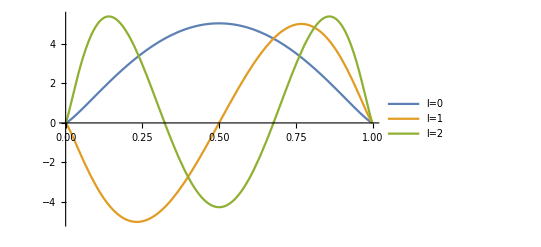

```mathematica
Plot[{χ[0,x],χ[1,x], χ[2,x]},{x,0,1},PlotLegends->{"l=0","l=1", "l=2"}]
```

```mathematica
ϕmom[n_,m_,q_]:=KAPPA^-1 √((4π (n!))/((n+Abs[m])!))(q/KAPPA)^Abs[m] Exp[-q^2/(2 KAPPA^2)]LaguerreL[n,Abs[m], q^2/KAPPA^2];
ϕmomAngle[m_,θ_]:=Exp[ⅈ m θ]

(*ϕmomFull[n_,m_,q_,θ_]:=ϕmom[n,m,q] ϕmomAngle[m,θ]*)

ϕpos[n_,m_,ρ_]:=If[ρ==0 && m == 0, 
KAPPA √(1/π),
KAPPA √((n!)/(π(n+Abs[m])!))(KAPPA ρ)^Abs[m] Exp[(-KAPPA^2 ρ^2)/2]LaguerreL[n,Abs[m], KAPPA^2 ρ^2]];
ϕposAngle[n_,m_,θ_]:=(-1)^(n+Abs[m]/2)  Exp[ⅈ m θ ]

(*ϕposFull[n_,m_,ρ_,θ_]:=ϕpos[n,m,ρ] ϕposAngle[n,m,θ]*)
```

```mathematica
LaguerreL[9,0, 0]
```

1

```mathematica
ϕposAngle[0,0,π/2]
```

1

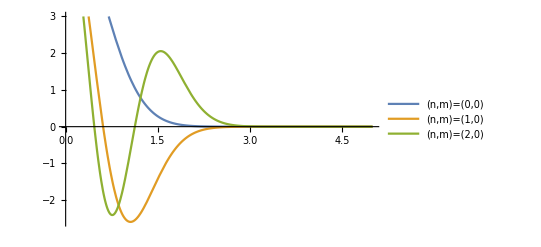

```mathematica
Plot[{ϕmom[0,0,q],ϕmom[1,0,q], ϕmom[2,0,q]},{q,0,5},PlotLegends->{"(n,m)=(0,0)","(n,m)=(1,0)", "(n,m)=(2,0)"}]
```

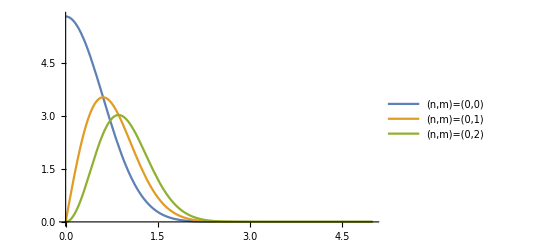

```mathematica
Plot[{ϕmom[0,0,q],ϕmom[0,1,q], ϕmom[0,2,q]},{q,0,5},PlotLegends->{"(n,m)=(0,0)","(n,m)=(0,1)", "(n,m)=(0,2)"}]
```

```mathematica
ϕpos[0,0,0.1]
```

0.343516

## LFWF in Momentum space:

```mathematica
ϕmomAngle[m,0]
```

1

```mathematica
LFWFmomBasis[k_,x_,{n_,m_,l_}]:=ϕmom[n,m,k/√(x(1-x))]χ[l,x]
LFWFmomBasisFull[k_,x_,θ_,{n_,m_,l_}]:=ϕmom[n,m,k/√(x(1-x))]χ[l,x ] ϕmomAngle[m,θ]
```

```mathematica
LFWFmomBasisFull[1,0.6,0.3,{0,0,0}]
```

0.103303

```mathematica
1/(2(2π)^3)  Sum[NIntegrate[k/(x(1-x)) Abs[ LFWFmomFull[k,x,t,{s1,s2},5]]^2,{k,0,Infinity},{x,0,1},{t,0,2π},Method->{"GlobalAdaptive", "MaxErrorIncreases"->20000, "SingularityHandler"-> "DuffyCoordinates"},
PrecisionGoal->8, AccuracyGoal->7],
{s1,-1,1,2},{s2,-1,1,2}](*normalization*)
```

0.944694

## LFWF in Position space:

```mathematica
ϕposAngle[n,m,0]
```

(-1)^(n+Abs[m]/2)

```mathematica
LFWFposBasis[r_,x_,{n_,m_,l_}]:=√(x(1-x))  ϕposAngle[n,m,0]ϕpos[n,m,√(x(1-x))r]χ[l,x];
LFWFposBasisFull[r_,x_,θ_,{n_,m_,l_}]:=If[x==0 ||x==1, 0,√(x(1-x))  ϕposAngle[n,m,θ]ϕpos[n,m,√(x(1-x))r]χ[l,x]]

Clear[LFWFposSquared];
LFWFposSquared[rx_,ry_,x_,{s1_,s2_},topk_:100,mj_:0,hadron_:1]:=Module[{bs,data,val,n,r,θ,amp},
data=state[mj,hadron];
(*bs =coeffspin[data,{s1,s2}];*)
bs=Sort[coeffspin[state[mj,hadron],{s1,s2}],Abs[#1[[6]]]≥Abs[#2[[6]]]&][[1;;topk]];
θ=Arg[rx+ⅈ  ry];
r=Sqrt[rx^2+ry^2];
amp=Sum[bs[[i,6]]*LFWFposBasisFull[r,x, θ,{bs[[i,1]],bs[[i,2]],bs[[i,3]]}],{i,1, Length[bs]}];
Abs[amp]^2
]
LFWFposSquaredSummed[rx_,ry_,x_,topk_:100,mj_:0,hadron_:1]:=LFWFposSquared[rx,ry,x,{1,1},topk,mj,hadron]+LFWFposSquared[rx,ry,x,{-1,1},topk,mj,hadron]+LFWFposSquared[rx,ry,x,{1,-1},topk,mj,hadron]+LFWFposSquared[rx,ry,x,{-1,-1},topk,mj,hadron]

checkNorm[lfwfsquareInterp_]:=Module[{},
NIntegrate[lfwfsquareInterp[rx,ry,x],{rx,-10,10},{ry,-10,10},{x,0,1}]/4/π
]
```

```mathematica
LFWFposBasisFull[3,0.1,0.3,{0,1,0}]
```

-0.0205337+0.0663799 ⅈ

```mathematica
Sort[coeffspin[state[0,1],{1,-1}],Abs[#1[[6]]]≥Abs[#2[[6]]]&][[1;;3]]
```

{{0,0,0,1,-1,0.442466},{1,0,0,1,-1,-0.234734},{0,0,2,1,-1,0.141855}}

```mathematica
LFWFposSquared[-0.1,0.9,0.2,{1,-1},4]
```

0.155492

## Small Grids: ~ 5000 points

## LFWF Squared, Spin=(1,-1) :

```mathematica
smallGridDir="LFWF_Squared_4851points";
```

```mathematica
lfwfSquareList=<<(ToFileName[{cwd,smallGridDir},"LFWF_Squared_Spin1m1_AllComponents_4851pts.dat"])
```

{{{-10,-10,0.},0.},{{-10,-10,0.1},0.000024292},{{-10,-10,0.2},0.0000334835},{{-10,-10,0.3},0.0000152155},{{-10,-10,0.4},5.62267×10^-6},{{-10,-10,0.5},3.83449×10^-6},4839,{{10,10,0.5},3.83449×10^-6},{{10,10,0.6},5.62267×10^-6},{{10,10,0.7},0.0000152155},{{10,10,0.8},0.0000334835},{{10,10,0.9},0.000024292},{{10,10,1.},0.}}
 |  |  |  |

```mathematica
Dimensions[lfwfSquareList]
```

{4851,2}

```mathematica
lfwfInterp=Interpolation[lfwfSquareList, Method->"Hermite", InterpolationOrder->10]
```

InterpolatingFunction[…]

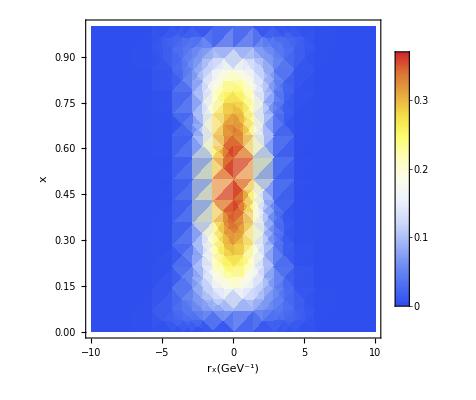

```mathematica
DensityPlot[lfwfInterp[rx,0,x],{rx,-10,10},{x,0.0,1.0}, ColorFunction-> "TemperatureMap",FrameLabel->{"r_x(GeV^-1)", "x"},PlotLegends->Automatic,PlotRange->Full]
```

```mathematica
Plot3D[lfwfInterp[rx,0,x],{x,0.0,1.0},{rx,-10,10}, ColorFunction-> "TemperatureMap",AxesLabel->Automatic,PlotLegends->Automatic,PlotRange->Full]
```

-Graphics3D-

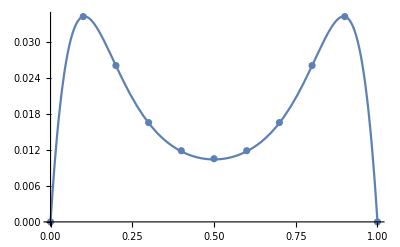

```mathematica
rx=0.12;ry=-3.554;
datalist=Table[{i/10,LFWFposSquared[rx,ry,i/10,{1,-1},100]},{i,0,10}];
Show[
Plot[lfwfInterp[rx,ry,x],{x,0.0,1.0}, PlotLegends->Automatic,PlotRange->Full],
ListPlot[datalist]
]
```

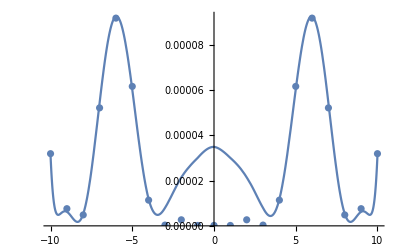

```mathematica
x=0.33;ry=5.5;
datalist=Table[{i,LFWFposSquared[i,ry,x,{1,-1},100]},{i,-10,10}];
Show[
Plot[lfwfInterp[rx,ry,x],{rx,-10,10}, PlotLegends->Automatic,PlotRange->Full],
ListPlot[datalist]
]
```

```mathematica
checkNorm[lfwfInterp]
```

$Aborted

## Large Grids: ~ 4,000,000 points

## LFWF Squared, Spin=(1,-1) :

```mathematica
largeGridDir="LFWF_Squared_4080501points";
lfwfSquareList2=<<(ToFileName[{cwd,largeGridDir},"LFWF_Squared_Spin1m1_4080501pts.dat"])
```

{1}
 |  |  |  |

```mathematica
Dimensions[lfwfSquareList2]
```

{201,201,101,2}

```mathematica
lfwfSquareList2 =Flatten[lfwfSquareList2,2]
```

{{{-10.,-10.,0.},0.},{{-10.,-10.,0.01},0.000114466},{{-10.,-10.,0.02},3.22059×10^-7},{{-10.,-10.,0.03},0.0000243083},{{-10.,-10.,0.04},0.0000169751},{{-10.,-10.,0.05},1.06305×10^-7},4080490,{{10.,10.,0.96},0.0000169751},{{10.,10.,0.97},0.0000243083},{{10.,10.,0.98},3.22059×10^-7},{{10.,10.,0.99},0.000114466},{{10.,10.,1.},0.}}
 |  |  |  |

```mathematica
Dimensions[lfwfSquareList2]
```

{4080501,2}

```mathematica
lfwfInterp2=Interpolation[lfwfSquareList2, Method->"Hermite", InterpolationOrder->3]
```

InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 1.}}, <>]

```mathematica
DensityPlot[lfwfInterp[rx,0,x],{rx,-10,10},{x,0.0,1.0}, ColorFunction-> "TemperatureMap",FrameLabel->{"r_x(GeV^-1)", "x"},PlotLegends->Automatic,PlotRange->Full]
```

-Graphics-

```mathematica
Plot3D[lfwfInterp[rx,0,x],{x,0.0,1.0},{rx,-10,10}, ColorFunction-> "TemperatureMap",AxesLabel->Automatic,PlotLegends->Automatic,PlotRange->Full]
```

-Graphics3D-

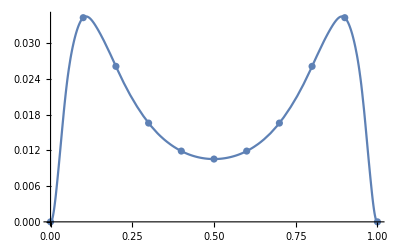

```mathematica
rx=0.12;ry=-3.554;
datalist=Table[{i/10,LFWFposSquared[rx,ry,i/10,{1,-1},100]},{i,0,10}];
Show[
Plot[lfwfInterp2[rx,ry,x],{x,0.0,1.0}, PlotLegends->Automatic,PlotRange->Full],
ListPlot[datalist]
]
```

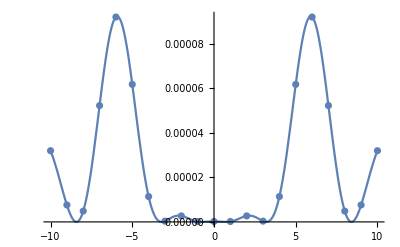

```mathematica
x=0.33;ry=5.5;
datalist=Table[{i,LFWFposSquared[i,ry,x,{1,-1},100]},{i,-10,10}];
Show[
Plot[lfwfInterp2[rx,ry,x],{rx,-10,10}, PlotLegends->Automatic,PlotRange->Full],
ListPlot[datalist]
]
```

```mathematica
checkNorm[lfwfInterp2]
```

$Aborted

## LFWF Squared, Combining spins

```mathematica
largeGridDir="LFWF_Squared_4080501points";
lfwfSquareList2=<<(ToFileName[{cwd,largeGridDir},"LFWF_Squared_Spin1m1_4080501pts.dat"])
```

{1}
 |  |  |  |

```mathematica
Dimensions[lfwfSquareList2]
```

{201,201,101,2}

```mathematica
largeGridDir="LFWF_Squared_4080501points";
lfwfSquareList3=<<(ToFileName[{cwd,largeGridDir},"LFWF_Squared_Spin11_4080501pts.dat"])
```

{1}
 |  |  |  |

```mathematica
largeGridDir="LFWF_Squared_4080501points";
lfwfSquareList4=<<(ToFileName[{cwd,largeGridDir},"LFWF_Squared_Spinm11_4080501pts.dat"])
```

{1}
 |  |  |  |

```mathematica
largeGridDir="LFWF_Squared_4080501points";
lfwfSquareList5=<<(ToFileName[{cwd,largeGridDir},"LFWF_Squared_Spinm1m1_4080501pts.dat"])
```

{1}
 |  |  |  |

```mathematica
lfwfSquareList2[[69,133,43]]
lfwfSquareList3[[69,133,43]]
lfwfSquareList4[[69,133,43]]
lfwfSquareList5[[69,133,43]]
```

{{-3.2,3.2,0.42},0.000540938}

{{-3.2,3.2,0.42},0.00527341}

{{-3.2,3.2,0.42},0.000540938}

{{-3.2,3.2,0.42},0.00527341}

```mathematica
SumLFWFSquare[r1_,r2_,xi_]:={lfwfSquareList2[[r1,r2,xi,1]],
Assert[lfwfSquareList2[[r1,r2,xi,1]]==lfwfSquareList3[[r1,r2,xi,1]]];
Assert[lfwfSquareList3[[r1,r2,xi,1]]==lfwfSquareList4[[r1,r2,xi,1]]];
Assert[lfwfSquareList4[[r1,r2,xi,1]]==lfwfSquareList5[[r1,r2,xi,1]]];
lfwfSquareList2[[r1,r2,xi,2]]+
lfwfSquareList3[[r1,r2,xi,2]]+
lfwfSquareList4[[r1,r2,xi,2]]+
lfwfSquareList5[[r1,r2,xi,2]]}
```

```mathematica
SumLFWFSquare[1,1,2]
```

{{-10.,-10.,0.01},0.000411061}

```mathematica
SumLFWFSquare[69,133,43]
```

{{-3.2,3.2,0.42},0.0116287}

```mathematica
summedLFWFSquareList =Table[SumLFWFSquare[r1,r2,xi],{r1, 1, 201},{r2,1,201},{xi,1,101}]
```

{1}
 |  |  |  |

```mathematica
summedLFWFSquareList[[69,133,43]]
```

{{-3.2,3.2,0.42},0.0116287}

```mathematica
flattenedSummedLFWFSquareList=Flatten[summedLFWFSquareList,2]
```

{{{-10.,-10.,0.},0.},{{-10.,-10.,0.01},0.000411061},{{-10.,-10.,0.02},0.000125457},{{-10.,-10.,0.03},0.0000486577},{{-10.,-10.,0.04},0.00008324},{{-10.,-10.,0.05},0.0000587306},4080489,{{10.,10.,0.95},0.0000587306},{{10.,10.,0.96},0.00008324},{{10.,10.,0.97},0.0000486577},{{10.,10.,0.98},0.000125457},{{10.,10.,0.99},0.000411061},{{10.,10.,1.},0.}}
 |  |  |  |

```mathematica
Dimensions[flattenedSummedLFWFSquareList]
```

{4080501,2}

### Discrete Points Normalization Check

```mathematica
Sum[flattenedSummedLFWFSquareList[[i,2]], {i,1,4080501}]
```

124957.

```mathematica
124957*(20/200)*(20/200)*(1/100)*1.0/4/π
```

0.994376

```mathematica
summedLFWFInterpolation=Interpolation[flattenedSummedLFWFSquareList, Method->"Hermite", InterpolationOrder->3]
```

InterpolatingFunction[{{-10., 10.}, {-10., 10.}, {0., 1.}}, <>]

### Visualization

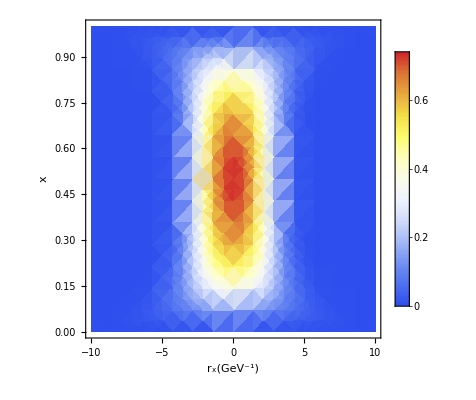

```mathematica
DensityPlot[summedLFWFInterpolation[rx,0,x],{rx,-10,10},{x,0.0,1.0}, ColorFunction-> "TemperatureMap",FrameLabel->{"r_x(GeV^-1)", "x"},PlotLegends->Automatic,PlotRange->Full]
```

```mathematica
Plot3D[summedLFWFInterpolation[rx,0,x],{x,0.0,1.0},{rx,-10,10}, ColorFunction-> "TemperatureMap",AxesLabel->Automatic,PlotLegends->Automatic,PlotRange->Full]
```

-Graphics3D-

### Output to files

```mathematica
cwd
```

C:\Users\WenyangQian\PROJECT_MASTER\Physics_物理\ppv2\Qian\LFWF_data\

```mathematica
summedLFWFSquareList>>cwd<>"summed_LFWF_squared_4080501points.dat"
```

```mathematica
summedLFWFInterpolation[0.1,0.1,0.1]
```

0.243835

```mathematica
Dimensions[summedLFWFSquareList]
```

{201,201,101,2}

```mathematica
summedLFWFSquareList[[1,1,1]]
```

{{-10.,-10.,0.},0.}

```mathematica
LFWFposSquaredSummed[0.1,0.1,0.1]
```

0.243835

### 1D Projection Check with Exact evaluation

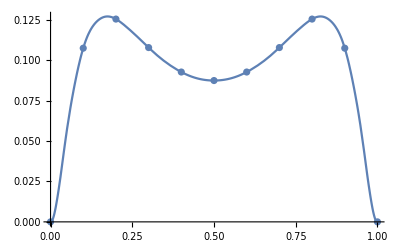

```mathematica
rx=0.12;ry=-3.554;
datalist=Table[{i/10,LFWFposSquaredSummed[rx,ry,i/10]},{i,0,10}];
Show[
Plot[summedLFWFInterpolation[rx,ry,x],{x,0.0,1.0}, PlotLegends->Automatic,PlotRange->Full],
ListPlot[datalist]
]
```

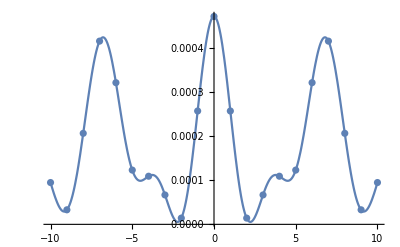

```mathematica
x=0.33;ry=5.5;
datalist=Table[{i,LFWFposSquaredSummed[i,ry,x]},{i,-10,10}];
Show[
Plot[summedLFWFInterpolation[rx,ry,x],{rx,-10,10}, PlotLegends->Automatic,PlotRange->Full],
ListPlot[datalist]
]
```

### Interpolation LFWF Normalization Check

```mathematica
checkNorm[summedLFWFInterpolation]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12.4952 and 0.0000236773 for the integral and error estimates.

0.994336